#### Soma Alternada

```mathematica
s[n_]=Sum[(-1)^(k-1)(1/k),{k,1,n}];
```

```mathematica
tables[n_]:=Table[(-1)^(k-1)(1/k),{k,1,n}];
```

```mathematica
tables[10]
```

{1,-1/2,1/3,-1/4,1/5,-1/6,1/7,-1/8,1/9,-1/10}

```mathematica
Limit[s[n],n->Infinity]
```

Log[2]

#### Soma sem alternar

```mathematica
s2[n_]=Sum[1/k,{k,1,n}];
```

```mathematica
tables2[n_]:=Table[1/k,{k,1,n}];
```

```mathematica
tables2[10]
```

{1,1/2,1/3,1/4,1/5,1/6,1/7,1/8,1/9,1/10}

```mathematica
Limit[s2[n],n->Infinity]
```

∞

```mathematica
f=√(2+#) &;
```

```mathematica
nestList[x_]:=NestList[f,√2,10]
```

```mathematica
list=N[nestList[5]];
```

```mathematica
t[n_]:=Nest[f,√2,n]
```

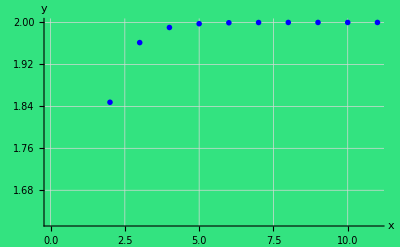

```mathematica
ListPlot[list,GridLines->Automatic,GridLinesStyle->{{Gray, Dotted}, {Gray, Dotted}},AxesLabel->{"x","y"},Background->RGBColor[0.2,0.89,0.5,0.56],PlotStyle->{PointSize[.01],Blue}]
```

```mathematica
TeXForm[HoldForm[∫_0^3 x ⅆx]];
```

```mathematica
N[Pi,40]
```

3.141592653589793238462643383279502884197

#### Série Harmônica

```mathematica
listPoints=ListPlot[Table[{x,1/x},{x,1,20}],GridLines->Automatic,GridLinesStyle->{{Gray,Dashed},{Gray,Dashed}}];
```

```mathematica
barList=BarChart[Table[1/x,{x,1,20}],ChartStyle->"Pastel"];
```

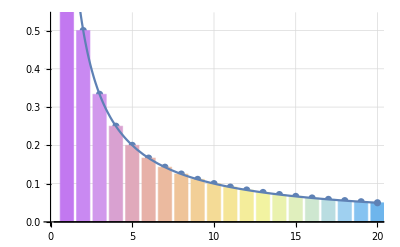

```mathematica
Show[listPoints,barList,Plot[1/x,{x,0,20}]]
```